```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small//Eurovision2019"];
```

```mathematica
LaunchKernels[8]
```

{KernelObject[17,local],KernelObject[18,local],KernelObject[19,local],KernelObject[20,local],KernelObject[21,local],KernelObject[22,local],KernelObject[23,local],KernelObject[24,local]}

```mathematica
kernels=ParallelTable[$KernelID->i,{i,$KernelCount}];
SetSharedVariable[kernels];SetSharedVariable[currentNumber]
currentNumber=ConstantArray[0,Length@kernels];
```

## Preparing cities

```mathematica
(*Import the city names*)
city2=Import["worldcitiespop.txt","CSV"];
```

```mathematica
(*Select only the ones with reasonasble populations*)
city2withpopulation=Select[city2,#[[5]]>10000&];
```

```mathematica
(* Number of entries in the total list*)
Length[city2]
```

3173959

```mathematica
(* Number of entries in the total list that have large populations*)
Length[city2withpopulation]
```

25077

```mathematica
(*First semifinal*)
ShortName={"cy","mn","fi","pl","si","cz","hu","by","rs","be","ge","au","is","ee","po","gr","sm","fr","il","es"};
LongName={"CYPRUS","MONTENEGRO","FINLAND","POLAND","SLOVENIA","CZECHIA","HUNGARY","BELARUS","SERBIA","BELGIUM","GEORGIA","AUSTRALIA","ICELAND","ESTONIA","PORTUGAL","GREECE","SAN MARINO","FRANCE","ISRAEL","SPAIN"};
LongNameForImport1=LongName;
LocalName={"Cipros","Crna","Suomi","Polska","Slovenia","Ceska","Magyarorszag","Bielarus","Srbija","Belgie","Sakartvelo","Australia","Island","Eesti","Portuguesa","Hellas","Marino","Francaise","Yisrael","Espana"};
```

```mathematica
(* Check that all have the same length *)
Length[ShortName]
Length[LongName]
Length[LocalName]
```

```mathematica
(* Check that short name and local name agree *)
{ShortName,LongName}//Transpose
```

{{ar,ARMENIA},{ie,IRELAND},{md,MOLDOVA},{ch,SWITZERLAND},{lv,LATVIA},{ro,ROMANIA},{de,DENMARK},{se,SWEDEN},{at,AUSTRIA},{hr,CROATIA},{mt,MALTA},{lt,LITHUANIA},{ru,RUSSIA},{al,ALBANIA},{no,NORWAY},{ne,NETHERLANDS},{mk,MACEDONIA},{az,AZERBAIJAN},{de,GERMANY},{it,ITALY},{gb,UK}}

```mathematica
(* Check that long name and local name agree *)
{LongName,LocalName}//Transpose
```

{{ARMENIA,Hayastan},{IRELAND,Ireland},{MOLDOVA,Moldova},{SWITZERLAND,Schweiz},{LATVIA,Latvija},{ROMANIA,Romania},{DENMARK,Danmark},{SWEDEN,Sverige},{AUSTRIA,Osterreich},{CROATIA,Hrvatska},{MALTA,Malta},{LITHUANIA,Lietuva},{RUSSIA,Rossiya},{ALBANIA,Shqiperi},{NORWAY,Norge},{NETHERLANDS,Nederland},{MACEDONIA,Makedonija},{AZERBAIJAN,Azerbaycan},{GERMANY,Deutschland},{ITALY,Italia},{UK,UK}}

```mathematica
Table[CityFromCountry=Reverse[SortBy[Select[city2withpopulation,#[[1]]==ShortName[[i]]&],#[[5]]&]];CityFromCountry100=If[Length[CityFromCountry]>100,CityFromCountry[[1;;100]],CityFromCountry];
Save[LongName[[i]],CityFromCountry100];,{i,Length[ShortName]}];
```

```mathematica
(* all cities for countries in the first semi *)
SearchNames1=Table[Join[{LongName[[i]]},{LocalName[[i]]},CityFromCountry=Get[LongName[[i]]];CityFromCountry[[All,3]]],{i,Length[LongName]}];
```

```mathematica
(*Second semifinal*)
ShortName={"ar","ie","md","ch","lv","ro","de","se","at","hr","mt","lt","ru","al","no","ne","mk","az","de","it","gb"};
LongName={"ARMENIA","IRELAND","MOLDOVA","SWITZERLAND","LATVIA","ROMANIA","DENMARK","SWEDEN","AUSTRIA","CROATIA","MALTA","LITHUANIA","RUSSIA","ALBANIA","NORWAY","NETHERLANDS","MACEDONIA","AZERBAIJAN","GERMANY","ITALY","UK"};
LongNameForImport2=LongName;
LocalName={"Hayastan","Ireland","Moldova","Schweiz","Latvija","Romania","Danmark","Sverige","Osterreich","Hrvatska","Malta","Lietuva","Rossiya","Shqiperi","Norge","Nederland","Makedonija","Azerbaycan","Deutschland","Italia","UK"};
```

```mathematica
(*If[$MachineName!="iapetus",SetDirectory["~/Documents/Astrodataiscool/Eurovision2016/Cities"],SetDirectory["/export/data1/caplarn/Documents/Small/Eurovision2016/Cities"];]*)
```

```mathematica
Table[CityFromCountry=Reverse[SortBy[Select[city2withpopulation,#[[1]]==ShortName[[i]]&],#[[5]]&]];CityFromCountry100=If[Length[CityFromCountry]>100,CityFromCountry[[1;;100]],CityFromCountry];
Save[LongName[[i]],CityFromCountry100];,{i,Length[ShortName]}];
```

```mathematica
(* all cities for countries in the second semi *)
SearchNames2=Table[Join[{LongName[[i]]},{LocalName[[i]]},CityFromCountry=Get[LongName[[i]]];CityFromCountry[[All,3]]],{i,Length[LongName]}];
```

```mathematica
(* Check that all have the same length *)
Length[ShortName]
Length[LongName]
Length[LocalName]
```

21

21

21

```mathematica
(* Check that short name and local name agree *)
{ShortName,LongName}//Transpose
```

{{ar,ARMENIA},{ie,IRELAND},{md,MOLDOVA},{ch,SWITZERLAND},{lv,LATVIA},{ro,ROMANIA},{de,DENMARK},{se,SWEDEN},{at,AUSTRIA},{hr,CROATIA},{mt,MALTA},{lt,LITHUANIA},{ru,RUSSIA},{al,ALBANIA},{no,NORWAY},{ne,NETHERLANDS},{mk,MACEDONIA},{az,AZERBAIJAN},{de,GERMANY},{it,ITALY},{gb,UK}}

```mathematica
(* Check that long name and local name agree *)
{LongName,LocalName}//Transpose
```

{{ARMENIA,Hayastan},{IRELAND,Ireland},{MOLDOVA,Moldova},{SWITZERLAND,Schweiz},{LATVIA,Latvija},{ROMANIA,Romania},{DENMARK,Danmark},{SWEDEN,Sverige},{AUSTRIA,Osterreich},{CROATIA,Hrvatska},{MALTA,Malta},{LITHUANIA,Lietuva},{RUSSIA,Rossiya},{ALBANIA,Shqiperi},{NORWAY,Norge},{NETHERLANDS,Nederland},{MACEDONIA,Makedonija},{AZERBAIJAN,Azerbaycan},{GERMANY,Deutschland},{ITALY,Italia},{UK,UK}}

```mathematica
SearchNames=Join[SearchNames1,SearchNames2];
```

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
Save["SearchNames",SearchNames];
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

## Preparation for the analysis - semi finals

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
hashtags={"#CYP","#MNE","#FIN","#POL","#SVN","#CZE","$HUN","#BLR","#SRB","#BEL","#GEO","#AUS","#ISL","#EST","#PRT","#GRC","#SMR"}
hashtags2={"#ARM","#IRL","#MDA","#CHE","#LVA","#ROU","#DNK","#SWE","#AUT","#HRV","#MLT","#LTU","#RUS","#ALB","#NOR","#NLD","#MKD","#AZE"}
```

{#CYP,#MNE,#FIN,#POL,#SVN,#CZE,$HUN,#BLR,#SRB,#BEL,#GEO,#AUS,#ISL,#EST,#PRT,#GRC,#SMR}

{#ARM,#IRL,#MDA,#CHE,#LVA,#ROU,#DNK,#SWE,#AUT,#HRV,#MLT,#LTU,#RUS,#ALB,#NOR,#NLD,#MKD,#AZE}

```mathematica
(*All the hashtags*)
hashtagsall=Join[hashtags,hashtags2]
```

{#CYP,#MNE,#FIN,#POL,#SVN,#CZE,$HUN,#BLR,#SRB,#BEL,#GEO,#AUS,#ISL,#EST,#PRT,#GRC,#SMR,#ARM,#IRL,#MDA,#CHE,#LVA,#ROU,#DNK,#SWE,#AUT,#HRV,#MLT,#LTU,#RUS,#ALB,#NOR,#NLD,#MKD,#AZE}

```mathematica
(*There are 35 countries in semifinals*)
Length[hashtagsall]
```

35

```mathematica
(*There are 17 countries in the first semifinal*)
Length[hashtags]
```

17

```mathematica
(* Import data for each country, named for its hashtag*)
RawTwitterData=Table[Import[ToLowerCase[StringDrop[hashtags[[i]],1]]<>".txt","Data"],{i,Length[hashtags]}];
Monitor[RawTwitterData=Table[{StringJoin[Table[RawTwitterData[[j,i]],{i,Length[RawTwitterData[[j]]]}]]},{j,Length[RawTwitterData]}];,j]
```

```mathematica
(* Import  data for each country, named for its full country name *)
```

```mathematica
RawTwitterDataEurovisionHashtag=Table[Import[ToString[LongNameForImport1[[i]]]<>".txt","Data"],{i,Length[hashtags]}];
Monitor[RawTwitterDataEurovisionHashtag=Table[{StringJoin[Table[RawTwitterDataEurovisionHashtag[[j,i]],{i,Length[RawTwitterDataEurovisionHashtag[[j]]]}]]},{j,Length[RawTwitterDataEurovisionHashtag]}];,j]
```

```mathematica
(* Connect the two tables *)
```

```mathematica
RawTwitterData=Table[{RawTwitterData[[i,1]]<>RawTwitterDataEurovisionHashtag[[i,1]]},{i,Length[RawTwitterDataEurovisionHashtag]}];
```

```mathematica
(*2nd*)
```

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
(* Import data for each country, named for its hashtag*)RawTwitterData2=Table[Import[ToLowerCase[StringDrop[hashtags2[[i]],1]]<>".txt","Data"],{i,Length[hashtags2]}];
Monitor[RawTwitterData2=Table[{StringJoin[Table[RawTwitterData2[[j,i]],{i,Length[RawTwitterData2[[j]]]}]]},{j,Length[RawTwitterData2]}];,j]
(* Import  data for each country, named for its full country name *)
```

```mathematica
RawTwitterData2EurovisionHashtag=Table[Import[ToString[LongNameForImport2[[i]]]<>".txt","Data"],{i,1,Length[hashtags2]}];
Monitor[RawTwitterData2EurovisionHashtag=Table[{StringJoin[Table[RawTwitterData2EurovisionHashtag[[j,i]],{i,Length[RawTwitterData2EurovisionHashtag[[j]]]}]]},{j,Length[RawTwitterData2EurovisionHashtag]}];,j]
```

```mathematica
Length[RawTwitterData2EurovisionHashtag]
```

18

```mathematica
(* Connect the two tables *)
```

```mathematica
RawTwitterData2=Table[{RawTwitterData2[[i,1]]<>RawTwitterData2EurovisionHashtag[[i,1]]},{i,Length[RawTwitterData2EurovisionHashtag]}];
```

```mathematica
(* Check lengths *)
Length[RawTwitterDataEurovisionHashtag]
Length[RawTwitterData2EurovisionHashtag]
```

17

18

#### Analysis

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
(* get the correct time *)
f[data_]:=Block[{},Breaks1=Prepend[StringPosition[data,"newline"][[1]][[All,1]],1];
Breaks2=Prepend[StringPosition[data,"newline"][[1]][[All,2]],-1];
testMathematica=ParallelTable[currentNumber[[$KernelID/.kernels]]=i;StringTake[data,{Breaks2[[i]]+2,Breaks2[[i+1]]}],{i,Length[Breaks2]-1}];
Monitor[testMathematicaFormated=DeleteCases[Table[Check[{DateList[DateString[{StringTake[testMathematica[[i]],{1,StringPosition[testMathematica[[i]],","][[1,1,1]]-1}][[1]],{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]],StringTake[testMathematica[[i]],{StringPosition[testMathematica[[i]],","][[1,1,1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]-1}],StringTake[testMathematica[[i]],{Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[2]]-1}]},0],{i,Length[testMathematica]}],0];,i];
TimesOfTweets=N[(Map[AbsoluteTime[#]&,testMathematicaFormated[[All,1]]]-AbsoluteTime[{2019,5,14,19,0,0}])/3600];
testLocations=DeleteCases[testMathematicaFormated[[All,2]],{""}];
testLocationsStrings=Map[ToString[#]&,testLocations];
CountriesHowMuchTheyTweeted={SearchNames1[[All,1]],Table[Length[DeleteCases[StringPosition[testLocationsStrings,SearchNames1[[i]],IgnoreCase->True],{}]],{i,Length[SearchNames1]}]}//Transpose;{testMathematicaFormated,TimesOfTweets,CountriesHowMuchTheyTweeted}]
```

```mathematica
AbsoluteTiming[PrintTemporary@Dynamic[currentNumber];
Monitor[DataReducedEurovisionAdded=Table[f[RawTwitterData[[j]]],{j,Length[RawTwitterData]}];,{i,j}]]
```

{315.939,Null}

```mathematica
Save["DataReducedEurovisionAdded",DataReducedEurovisionAdded];
```

```mathematica
f2[data_]:=Block[{},Breaks1=Prepend[StringPosition[data,"newline"][[1]][[All,1]],1];
Breaks2=Prepend[StringPosition[data,"newline"][[1]][[All,2]],-1];
testMathematica=ParallelTable[currentNumber[[$KernelID/.kernels]]=i;StringTake[data,{Breaks2[[i]]+2,Breaks2[[i+1]]}],{i,Length[Breaks2]-1}];
Monitor[testMathematicaFormated=DeleteCases[Table[Check[{DateList[DateString[{StringTake[testMathematica[[i]],{1,StringPosition[testMathematica[[i]],","][[1,1,1]]-1}][[1]],{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]],StringTake[testMathematica[[i]],{StringPosition[testMathematica[[i]],","][[1,1,1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]-1}],StringTake[testMathematica[[i]],{Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[2]]-1}]},0],{i,Length[testMathematica]}],0],i]
TimesOfTweets=N[(Map[AbsoluteTime[#]&,testMathematicaFormated[[All,1]]]-AbsoluteTime[{2019,5,16,19,0,0}])/3600];
testLocations=DeleteCases[testMathematicaFormated[[All,2]],{""}];
testLocationsStrings=Map[ToString[#]&,testLocations];
CountriesHowMuchTheyTweeted={SearchNames2[[All,1]],Table[Length[DeleteCases[StringPosition[testLocationsStrings,SearchNames2[[i]],IgnoreCase->True],{}]],{i,Length[SearchNames2]}]}//Transpose;{testMathematicaFormated,TimesOfTweets,CountriesHowMuchTheyTweeted}]
```

```mathematica
AbsoluteTiming[PrintTemporary@Dynamic[currentNumber];
Monitor[DataReduced2EurovisionAdded=Table[f2[RawTwitterData2[[j]]],{j,Length[RawTwitterData2]}];,{i,j}]]
```

{286.709,Null}

```mathematica
Save["DataReduced2EurovisionAdded",DataReduced2EurovisionAdded];
```

### Firing plots

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Get["DataReducedEurovisionAdded"];Get["DataReduced2EurovisionAdded"];
DataReduced2=DataReduced2EurovisionAdded;
DataReduced=DataReducedEurovisionAdded;
```

```mathematica
SetDirectory[];
PlotOptions1={Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{25,FontFamily->"Helvetica"}};
fS=20;
pDisco[col_,testo_]={Graphics[{col,Thickness[0.1],Disk[{0.6,0.2},0.7]},ImageSize-> 40,PlotRange-> {{-2,2},{-2,2}}],Text[Style[testo,fS,FontFamily->"Helvetica"]]};
pRectangle[col_,testo_]={Graphics[{col,Thickness[0.1],Rectangle[{0,0}]},ImageSize-> 40,PlotRange-> {{-2,2},{-2,2}}],Text[Style[testo,fS,FontFamily->"Helvetica"]]};
linea[col_,ltype_,n_,t_,testo_]:={Graphics[{col,ltype,Opacity[n],Thickness[t],Line[{{0,-0.4},{1,-0.4}}]},ImageSize-> 40,AspectRatio-> 0.1],Text[Style[testo,fS,FontFamily->"Helvetica"]]};
```

```mathematica
Colors={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-};
Colors2={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255]};
```

```mathematica
int=Table[Interpolation[{Table[i+0.01,{i,-1,3.48,0.02}],BinCounts[DataReducedEurovisionAdded[[j,2]],{-1,3.5,0.02}]}//Transpose],{j,Length[DataReducedEurovisionAdded]}];
intButNoInt=Table[{Table[i+0.01,{i,-1,3.48,0.02}],BinCounts[DataReducedEurovisionAdded[[j,2]],{-1,3.5,0.02}]}//Transpose,{j,Length[DataReducedEurovisionAdded]}];
TableOfMax=Table[Select[intButNoInt[[i]],#[[2]]==Max[intButNoInt[[i]]]&][[1]],{i,Length[DataReducedEurovisionAdded]}];
```

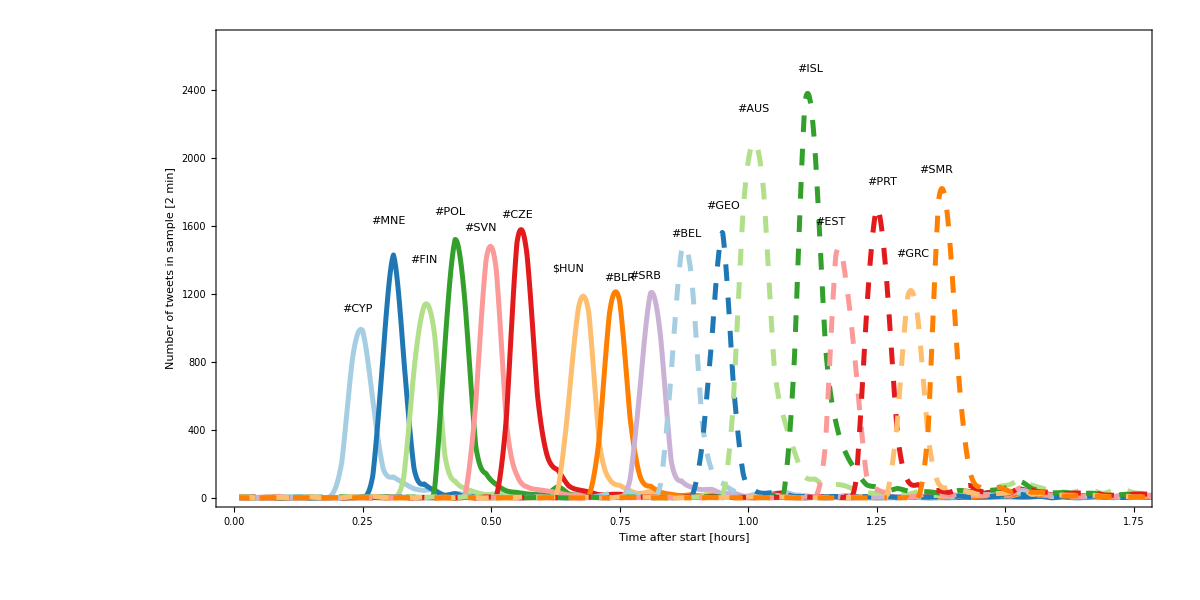

```mathematica
CustomOffset={{0,-20},{0,50},{+0.01,120},{0.00,10},{0.0,40},{+0.01,20},{-0.01,80},{0.01,-10},{0,-50},{0.02,-50},{0.01,0},{0.01,+50},{0.02,50},{0.00,50},{0.02,0},{0.02,100},{0.005,30},{0.0,0},{0.02,30}};

(* Have to adjust here, remove or add countries so that you have the correct number, as it happened in first semi*)
SF1=Plot[{int[[1]][x],int[[2]][x],int[[3]][x],int[[4]][x],int[[5]][x],int[[6]][x],int[[7]][x],int[[8]][x],int[[9]][x],int[[10]][x],int[[11]][x],int[[12]][x],int[[13]][x],int[[14]][x],int[[15]][x],int[[16]][x],int[[17]][x]},{x,0.01,2.5},PlotRange->{{0,1.75},{0,2700}},ImageSize->1200,AspectRatio->1/2,PlotStyle->{{Thickness[0.003],RGBColor[166/255,206/255,227/255]},{Thickness[0.003],RGBColor[31/255,120/255,180/255]},{Thickness[0.003],RGBColor[178/255,223/255,138/255]},{Thickness[0.003],RGBColor[51/255,160/255,44/255]},{Thickness[0.003],RGBColor[251/255,154/255,153/255]},{Thickness[0.003],RGBColor[227/255,26/255,28/255]},{Thickness[0.003],RGBColor[253/255,191/255,111/255]},{Thickness[0.003],RGBColor[255/255,127/255,0/255]},{Thickness[0.003],RGBColor[202/255,178/255,214/255]},{Thickness[0.003],RGBColor[166/255,206/255,227/255],Dashing[0.01]},{Thickness[0.003],RGBColor[31/255,120/255,180/255],Dashing[0.01]},{Thickness[0.003],RGBColor[178/255,223/255,138/255],Dashing[0.01]},{Thickness[0.003],RGBColor[51/255,160/255,44/255],Dashing[0.01]},{Thickness[0.003],RGBColor[251/255,154/255,153/255],Dashing[0.01]},{Thickness[0.003],RGBColor[227/255,26/255,28/255],Dashing[0.01]},{Thickness[0.003],RGBColor[253/255,191/255,111/255],Dashing[0.01]},{Thickness[0.003],RGBColor[255/255,127/255,0/255],Dashing[0.01]},{Thickness[0.003],RGBColor[202/255,178/255,214/255],Dashing[0.01]},{Thickness[0.003],RGBColor[166/255,206/255,227/255]}},FrameLabel->{"Time after start [hours]","Number of tweets in sample [2 min]","Eurovision 2019, Semi-final 1"},{FrameTicks->{LinTicks,LinTicks,None,None},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{Black,25,FontFamily->"Helvetica"}},Epilog->Table[Inset[Text[Style[hashtags[[i]],FontSize->15,Bold,Colors[[i]]]],{TableOfMax[[i,1]]-0.01+CustomOffset[[i,1]],150+CustomOffset[[i,2]]+TableOfMax[[i,2]]}],{i,Length[hashtags]}]]
```

```mathematica
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/SF1Plus200.png",SF1,ImageResolution->200];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/SF1Plus100.png",SF1,ImageResolution->100];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/SF1Plus50.png",SF1,ImageResolution->50];
```

```mathematica
int=Table[Interpolation[{Table[i+0.01,{i,-1,3.48,0.02}],BinCounts[DataReducedEurovisionAdded[[j,2]],{-1,3.5,0.02}]}//Transpose],{j,Length[DataReducedEurovisionAdded]}];
intButNoInt=Table[{Table[i+0.01,{i,-1,3.48,0.02}],BinCounts[DataReducedEurovisionAdded[[j,2]],{-1,3.5,0.02}]}//Transpose,{j,Length[DataReducedEurovisionAdded]}];
TableOfMax=Table[Select[intButNoInt[[i]],#[[2]]==Max[intButNoInt[[i]]]&][[1]],{i,Length[DataReducedEurovisionAdded]}];
```

```mathematica
OffsetDueToWrongBefore=0;
int=Table[Interpolation[{Table[i+0.01,{i,0,2.48,0.02}],BinCounts[DataReduced2EurovisionAdded[[j,2]],{OffsetDueToWrongBefore+0,OffsetDueToWrongBefore+2.5,0.02}]}//Transpose],{j,Length[DataReduced2EurovisionAdded]}];
intButNoInt=Table[{Table[i+0.01,{i,0,2.48,0.02}],BinCounts[DataReduced2EurovisionAdded[[j,2]],{OffsetDueToWrongBefore+0,OffsetDueToWrongBefore+2.5,0.02}]}//Transpose,{j,Length[DataReduced2EurovisionAdded]}];
TableOfMax=Table[Select[intButNoInt[[i]],#[[2]]==Max[intButNoInt[[i]]]&][[1]],{i,18}];
```

{{-0.02,0},{0,50},{0.,40},{0.01,40},{0.02,40},{0,80},{0.,40},{0.01,20},{0,-20},{0.02,100},{0.01,0},{0.01,0},{0.02,40},{0.,90},{0.,-30},{0,0},{0.02,0},{0.02,0}}

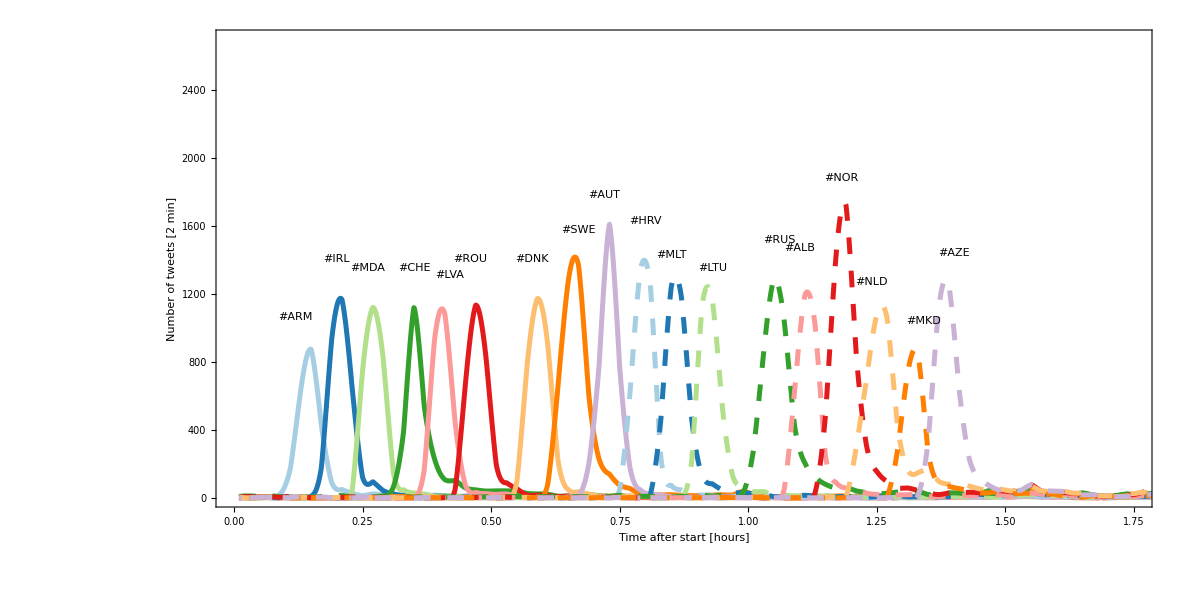

```mathematica
CustomOffset2={{-0.02,0},{0,50},{0.0,40},{0.01,40},{0.02,40},{0,80},{0.00,40},{0.01,20},{0,-20},{0.02,100},{0.01,0},{0.01,0},{0.02,40},{0.00,90},{0.00,-30},{0,0},{0.02,0},{0.02,0}}
SF2=Plot[{int[[1]][x],int[[2]][x],int[[3]][x],int[[4]][x],int[[5]][x],int[[6]][x],int[[7]][x],int[[8]][x],int[[9]][x],int[[10]][x],int[[11]][x],int[[12]][x],int[[13]][x],int[[14]][x],int[[15]][x],int[[16]][x],int[[17]][x],int[[18]][x]},{x,0.01,2.5},PlotRange->{{0,1.75},{0,2700}},ImageSize->1200,AspectRatio->1/2,PlotStyle->{{Thickness[0.003],RGBColor[166/255,206/255,227/255]},{Thickness[0.003],RGBColor[31/255,120/255,180/255]},{Thickness[0.003],RGBColor[178/255,223/255,138/255]},{Thickness[0.003],RGBColor[51/255,160/255,44/255]},{Thickness[0.003],RGBColor[251/255,154/255,153/255]},{Thickness[0.003],RGBColor[227/255,26/255,28/255]},{Thickness[0.003],RGBColor[253/255,191/255,111/255]},{Thickness[0.003],RGBColor[255/255,127/255,0/255]},{Thickness[0.003],RGBColor[202/255,178/255,214/255]},{Thickness[0.003],RGBColor[166/255,206/255,227/255],Dashing[0.01]},{Thickness[0.003],RGBColor[31/255,120/255,180/255],Dashing[0.01]},{Thickness[0.003],RGBColor[178/255,223/255,138/255],Dashing[0.01]},{Thickness[0.003],RGBColor[51/255,160/255,44/255],Dashing[0.01]},{Thickness[0.003],RGBColor[251/255,154/255,153/255],Dashing[0.01]},{Thickness[0.003],RGBColor[227/255,26/255,28/255],Dashing[0.01]},{Thickness[0.003],RGBColor[253/255,191/255,111/255],Dashing[0.01]},{Thickness[0.003],RGBColor[255/255,127/255,0/255],Dashing[0.01]},{Thickness[0.003],RGBColor[202/255,178/255,214/255],Dashing[0.01]}},FrameLabel->{"Time after start [hours]","Number of tweets [2 min]","Eurovision 2019, Semi-final 2"},{Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[30],LabelStyle->{Black,25,FontFamily->"Helvetica"}},Epilog->Table[Inset[Text[Style[hashtags2[[i]],FontSize->15,Bold,Colors2[[i]]]],{TableOfMax[[i,1]]-0.01+CustomOffset2[[i,1]],190+CustomOffset2[[i,2]]+TableOfMax[[i,2]]}],{i,18}]]
```

```mathematica
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/SF2Plus200.png",SF2,ImageResolution->200];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/SF2Plus100.png",SF2,ImageResolution->100];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/SF2Plus50.png",SF2,ImageResolution->50];
```

## Analysis - Semi finals

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
Get["DataReducedEurovisionAdded"];Get["DataReduced2EurovisionAdded"];
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
DataReduced2=DataReduced2EurovisionAdded;
DataReduced=DataReducedEurovisionAdded;
```

Number of tweets per each country

```mathematica
(* It goes to 41, because that is the length of the dataset, Length[DataReduced]*)
NumberOfTweets1={Table[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[i]][[All,1]][[1]],{i,Length[SearchNames1]}],Table[Total[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[i]][[All,2]]],{i,Length[SearchNames1]}]}//Transpose
(*ConstantArray[0,3] to take care of the countries that did not take part, 3 in the first semifinal of 2019*)
NumberOfTweetsWithoutOwn1={NumberOfTweets1[[All,1]],NumberOfTweets1[[All,2]]-Join[Table[DataReduced[[i,3,i,2]],{i,Length[DataReduced]}],ConstantArray[0,3]]}//Transpose
```

{{CYPRUS,470},{MONTENEGRO,99},{FINLAND,1861},{POLAND,1241},{SLOVENIA,573},{CZECHIA,122},{HUNGARY,317},{BELARUS,213},{SERBIA,1850},{BELGIUM,2520},{GEORGIA,248},{AUSTRALIA,3092},{ICELAND,647},{ESTONIA,171},{PORTUGAL,1281},{GREECE,931},{SAN MARINO,2},{FRANCE,1551},{ISRAEL,360},{SPAIN,2648}}

{{CYPRUS,238},{MONTENEGRO,66},{FINLAND,1581},{POLAND,1010},{SLOVENIA,452},{CZECHIA,93},{HUNGARY,263},{BELARUS,185},{SERBIA,1473},{BELGIUM,2254},{GEORGIA,210},{AUSTRALIA,2398},{ICELAND,436},{ESTONIA,133},{PORTUGAL,831},{GREECE,743},{SAN MARINO,2},{FRANCE,1551},{ISRAEL,360},{SPAIN,2648}}

```mathematica
(* Save for later use *)
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Save["NumberOfTweets1",NumberOfTweets1];
Save["NumberOfTweetsWithoutOwn1",NumberOfTweetsWithoutOwn1];
```

```mathematica
(* Go across the second semifinal*)
NumberOfTweets2={Table[GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[i]][[All,1]][[1]],{i,Length[SearchNames2]}],Table[Total[GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[i]][[All,2]]],{i,Length[SearchNames2]}]}//Transpose
NumberOfTweetsWithoutOwn2={NumberOfTweets2[[All,1]],NumberOfTweets2[[All,2]]-Join[Table[DataReduced2[[i,3,i,2]],{i,Length[DataReduced2]}],ConstantArray[0,3]]}//Transpose
```

{{ARMENIA,301},{IRELAND,1024},{MOLDOVA,15},{SWITZERLAND,956},{LATVIA,137},{ROMANIA,114},{DENMARK,2847},{SWEDEN,1035},{AUSTRIA,751},{CROATIA,369},{MALTA,253},{LITHUANIA,134},{RUSSIA,481},{ALBANIA,51},{NORWAY,2239},{NETHERLANDS,4605},{MACEDONIA,162},{AZERBAIJAN,92},{GERMANY,3956},{ITALY,1500},{UK,9001}}

{{ARMENIA,274},{IRELAND,734},{MOLDOVA,12},{SWITZERLAND,797},{LATVIA,106},{ROMANIA,82},{DENMARK,2652},{SWEDEN,816},{AUSTRIA,654},{CROATIA,283},{MALTA,99},{LITHUANIA,70},{RUSSIA,349},{ALBANIA,18},{NORWAY,1983},{NETHERLANDS,3965},{MACEDONIA,44},{AZERBAIJAN,58},{GERMANY,3956},{ITALY,1500},{UK,9001}}

```mathematica
(* Save for later use *)
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Save["NumberOfTweets2",NumberOfTweets2];
Save["NumberOfTweetsWithoutOwn2",NumberOfTweetsWithoutOwn2];
```

```mathematica
(* Join two total number of tweets to have all countries and save *)
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
NumberOfTweets=Join[NumberOfTweetsWithoutOwn1,NumberOfTweetsWithoutOwn2]
Save["NumberOfTweets",NumberOfTweets];
```

{{CYPRUS,238},{MONTENEGRO,66},{FINLAND,1581},{POLAND,1010},{SLOVENIA,452},{CZECHIA,93},{HUNGARY,263},{BELARUS,185},{SERBIA,1473},{BELGIUM,2254},{GEORGIA,210},{AUSTRALIA,2398},{ICELAND,436},{ESTONIA,133},{PORTUGAL,831},{GREECE,743},{SAN MARINO,2},{FRANCE,1551},{ISRAEL,360},{SPAIN,2648},{ARMENIA,274},{IRELAND,734},{MOLDOVA,12},{SWITZERLAND,797},{LATVIA,106},{ROMANIA,82},{DENMARK,2652},{SWEDEN,816},{AUSTRIA,654},{CROATIA,283},{MALTA,99},{LITHUANIA,70},{RUSSIA,349},{ALBANIA,18},{NORWAY,1983},{NETHERLANDS,3965},{MACEDONIA,44},{AZERBAIJAN,58},{GERMANY,3956},{ITALY,1500},{UK,9001}}

```mathematica
(* Join two total number of tweets, normalize per semifinal and save *)
```

```mathematica
NumberOfTweetsWithoutOwn1Normalized=NumberOfTweetsWithoutOwn1 ;
NumberOfTweetsWithoutOwn1Normalized[[All,2]]=NumberOfTweetsWithoutOwn1Normalized[[All,2]]/Total[NumberOfTweetsWithoutOwn1[[All,2]]];
```

```mathematica
NumberOfTweetsWithoutOwn2Normalized=NumberOfTweetsWithoutOwn2 ;
NumberOfTweetsWithoutOwn2Normalized[[All,2]]=NumberOfTweetsWithoutOwn2Normalized[[All,2]]/Total[NumberOfTweetsWithoutOwn2[[All,2]]];
```

```mathematica
(* Check number of tweets in each semifinal*)
Total[NumberOfTweetsWithoutOwn1[[All,2]]]
Total[NumberOfTweetsWithoutOwn2[[All,2]]]
```

16927

27453

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
NumberOfTweets=Join[NumberOfTweetsWithoutOwn1Normalized,NumberOfTweetsWithoutOwn2Normalized];
Save["NumberOfTweets",NumberOfTweets];
```

Get all tweets from a single country, select on the end only those which voted in this semi

```mathematica
(* Get voting patterns for first semifinal *)
Fractions1=Table[Help=Select[Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3],#[[3]]≠hashtags[[j]]&];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}}];
```

```mathematica
(* Get voting patterns for second semifinal *)
Fractions2=Table[Help=Select[Partition[Flatten[{GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[j]],hashtags2}//Transpose],3],#[[3]]≠hashtags2[[j]]&];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets2[[j,2]]],4]//Transpose,{j,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18}}];
```

```mathematica
(* Different defintions for points, depending on the number of countries that year*)
Points15={12,10,8,7,6,5,4,3,2,1,0,0,0,0,0};
Points16={12,10,8,7,6,5,4,3,2,1,0,0,0,0,0,0};
Points17={12,10,8,7,6,5,4,3,2,1,0,0,0,0,0,0,0};
Points18={12,10,8,7,6,5,4,3,2,1,0,0,0,0,0,0,0,0};
Points19={12,10,8,7,6,5,4,3,2,1,0,0,0,0,0,0,0,0,0};
```

```mathematica
Reverse[Sort[Fractions1[[1]],#1[[4]]<#2[[4]]&]][[All,3]]
```

{#GRC,#AUS,#ISL,#PRT,#BLR,#SMR,#SVN,#POL,#FIN,#CZE,$HUN,#SRB,#EST,#BEL,#GEO,#MNE}

```mathematica
(*Use Points with one smaller number than the number of countries in the semifinal, e.g., Points16 if there were 17 countries*)
SemiFinals1=Flatten[Table[{Reverse[Sort[Fractions1[[i]],#1[[4]]<#2[[4]]&]][[All,3]],Points16}//Transpose,{i,17}],1];
GatherSemiFinals1=GatherBy[SemiFinals1,First];
```

```mathematica
(* Points in semifinal 1*)
PointsSemi1=Reverse[SortBy[Table[{GatherSemiFinals1[[i,1,1]],2*Total[GatherSemiFinals1[[i]][[All,2]]]},{i,Length[GatherSemiFinals1]}],#[[2]]&]]
```

{{#ISL,312},{#AUS,306},{#PRT,168},{#POL,148},{#SMR,142},{#CZE,136},{#BEL,104},{#SVN,100},{#SRB,84},{#CYP,84},{#MNE,78},{#EST,68},{$HUN,62},{#GRC,58},{#FIN,56},{#BLR,38},{#GEO,28}}

```mathematica
SemiFinals2=Flatten[Table[{Reverse[Sort[Fractions2[[i]],#1[[4]]<#2[[4]]&]][[All,3]],Points17}//Transpose,{i,18}],1];
GatherSemiFinals2=GatherBy[SemiFinals2,First];
```

```mathematica
(* Points in semifinal 2 *)
PointsSemi2=Reverse[SortBy[Table[{GatherSemiFinals2[[i,1,1]],2*Total[GatherSemiFinals2[[i]][[All,2]]]},{i,Length[GatherSemiFinals2]}],#[[2]]&]]
```

{{#RUS,272},{#NOR,272},{#SWE,242},{#CHE,148},{#AZE,146},{#MLT,140},{#AUT,108},{#HRV,104},{#NLD,102},{#ARM,92},{#ALB,92},{#IRL,90},{#LTU,80},{#LVA,72},{#DNK,62},{#MDA,30},{#MKD,20},{#ROU,16}}

#### Plots

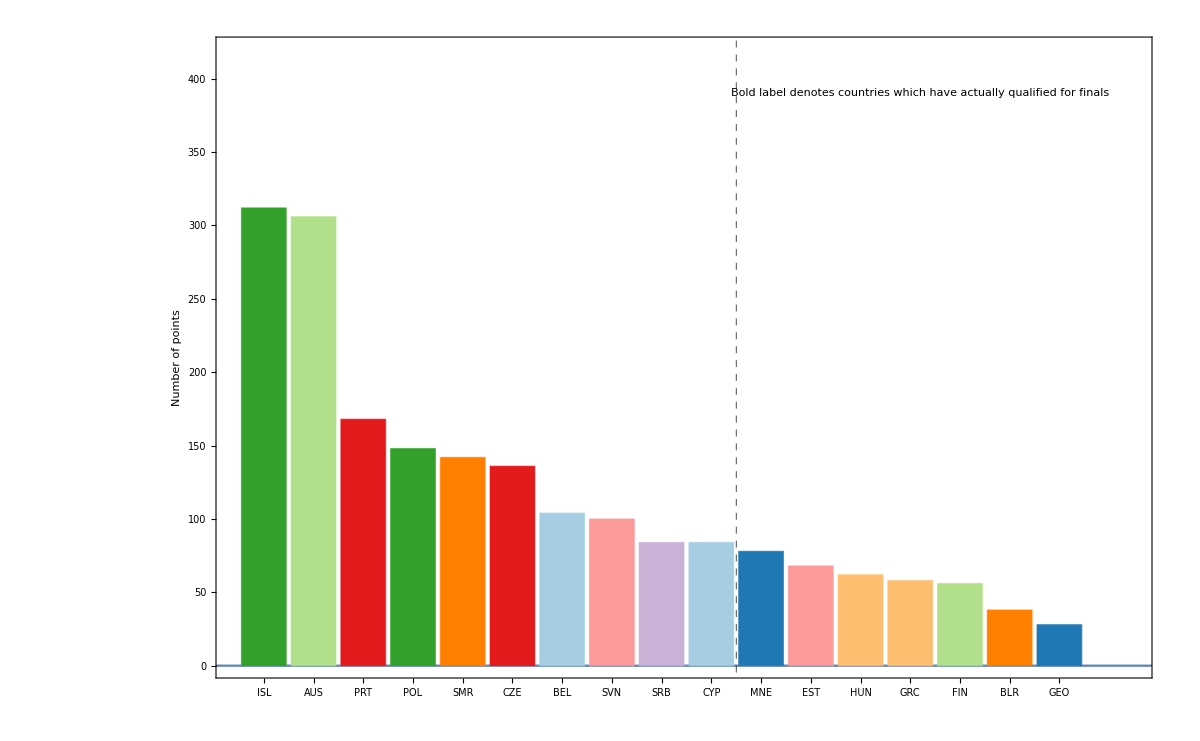

```mathematica
(*Have to modify here, to bolden the countries that have actually passed*)
Q1={1,2,5,6,8,9,10,12,14,16};
PSF1=Show[Plot[0,{x,0,20},GridLines->{{10.5},{}},GridLinesStyle->Directive[Black,Dashed,Thick], PlotRange->{{0.4,18.5},{0,420}},ImageSize->1200,AxesOrigin->{0,0},{FrameTicks->{{Automatic,None},{Table[{i,Style[StringTake[hashtags[[Flatten[Position[hashtags,PointsSemi1[[i,1]]]]]][[1]],{2,4}],If[MemberQ[Q1,i],Bold,Plain]],{0.00,0},Dashing[1]},{i,Length[hashtags]}],None}},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{Black,25,FontFamily->"Helvetica"}},FrameLabel->{"","Number of points","Predicted number of points for semi-final 1"},Epilog->Inset[Text[Style["Bold label denotes countries which have actually qualified for finals",FontSize->15,Plain,Black,FontFamily->"Helvetica"]],{14.2,390}]],BarChart[PointsSemi1[[All,2]],ChartStyle->{Table[EdgeForm[{Dashing[2],Thick}],{i,18}],Table[Colors[[Position[hashtags,PointsSemi1[[i,1]]][[1,1]]]],{i,Length[hashtags]}]},ImageSize->1200,BaseStyle->{FontFamily->"Helvetica",18},Frame->True,FrameStyle->Directive[Thick,Dashing[2]]],Plot[-10,{x,0,20},GridLines->{{10},{10}}]]
```

```mathematica
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/PSF1Plus200.png",PSF1,ImageResolution->200];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/PSF1Plus100.png",PSF1,ImageResolution->100];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/PSF1Plus50.png",PSF1,ImageResolution->50];
```

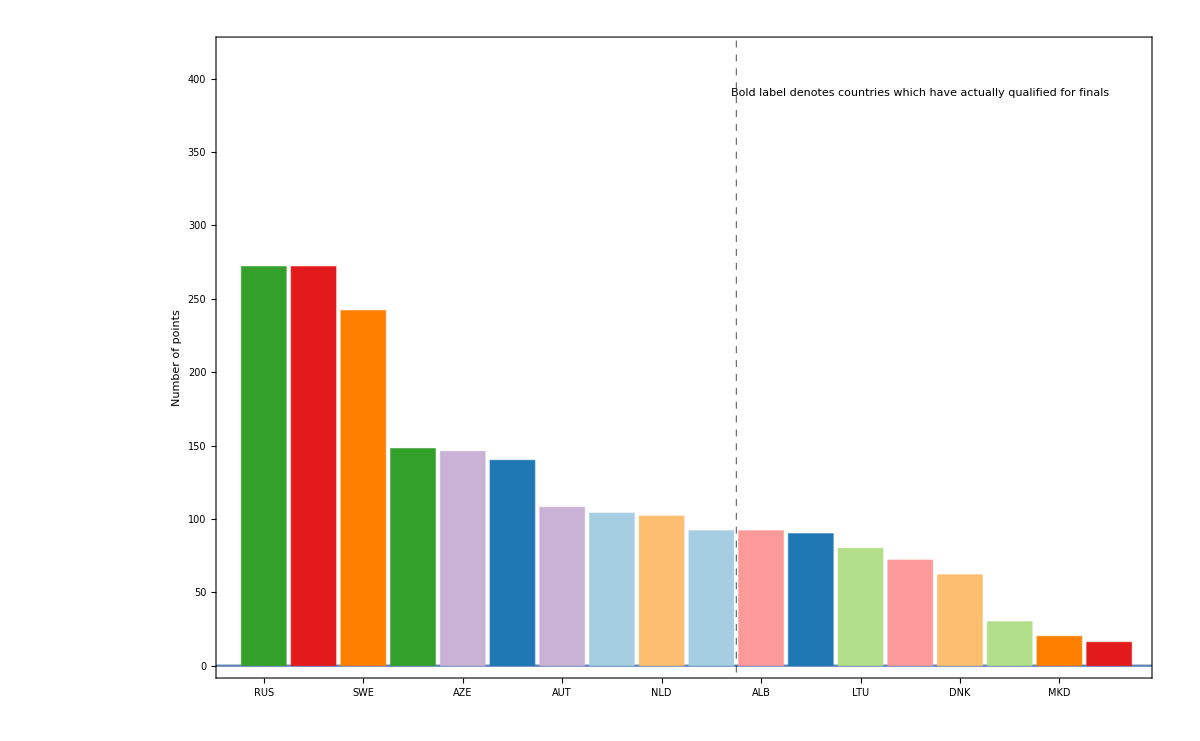

```mathematica
(*Have to modify here*)
Q2={1,2,3,4,5,6,9,11,15,17};
PSF2=Show[Plot[0,{x,0,20},GridLines->{{10.5},{}},GridLinesStyle->Directive[Black,Dashed,Thick], PlotRange->{{0.4,18.5},{0,420}},ImageSize->1200,AxesOrigin->{0,0},{FrameTicks->{{Automatic,None},{Table[{i,Style[StringTake[hashtags2[[Flatten[Position[hashtags2,PointsSemi2[[i,1]]]]]][[1]],{2,4}],If[MemberQ[Q2,i],Bold,Plain]],{0.00,0},Dashing[1]},{i,18}],None}},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{Black,25,FontFamily->"Helvetica"}},FrameLabel->{"","Number of points","Predicted number of points for semi-final 2"},Epilog->Inset[Text[Style["Bold label denotes countries which have actually qualified for finals",FontSize->15,Plain,Black,FontFamily->"Helvetica"]],{14.2,390}]],BarChart[PointsSemi2[[All,2]],ChartStyle->{Table[If[MemberQ[Q2,i],EdgeForm[{Dashing[2],Thick}],EdgeForm[{Dashing[2],Thick}]],{i,18}],Table[If[MemberQ[Q2,i],Colors[[Position[hashtags2,PointsSemi2[[i,1]]][[1,1]]]],Colors[[Position[hashtags2,PointsSemi2[[i,1]]][[1,1]]]]],{i,18}]},ImageSize->1200,BaseStyle->{FontFamily->"Helvetica",18},Frame->True,FrameStyle->Directive[Thick,Dashing[2]]],Plot[-10,{x,0,20},GridLines->{{10},{10}}]]
```

```mathematica
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/PSF2Plus200.png",PSF2,ImageResolution->200];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/PSF2Plus100.png",PSF2,ImageResolution->100];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/PSF2Plus50.png",PSF2,ImageResolution->50];
```

## Preparation for the analysis - for the final

```mathematica
(*additional redefinitions and  prep for the final = main change from before is the inclusion of the 6 countries*)
```

```mathematica
hashtags={"#CYP","#MNE","#FIN","#POL","#SVN","#CZE","$HUN","#BLR","#SRB","#BEL","#GEO","#AUS","#ISL","#EST","#PRT","#GRC","#SMR","#FRA","#ISR","#ESP"}
hashtags2={"#ARM","#IRL","#MDA","#CHE","#LVA","#ROU","#DNK","#SWE","#AUT","#HRV","#MLT","#LTU","#RUS","#ALB","#NOR","#NLD","#MKD","#AZE","#GER","#ITA","#GBR"}
```

{#CYP,#MNE,#FIN,#POL,#SVN,#CZE,$HUN,#BLR,#SRB,#BEL,#GEO,#AUS,#ISL,#EST,#PRT,#GRC,#SMR,#FRA,#ISR,#ESP}

{#ARM,#IRL,#MDA,#CHE,#LVA,#ROU,#DNK,#SWE,#AUT,#HRV,#MLT,#LTU,#RUS,#ALB,#NOR,#NLD,#MKD,#AZE,#GER,#ITA,#GBR}

```mathematica
(*All the hashtags*)
hashtagsall=Join[hashtags,hashtags2]
```

{#CYP,#MNE,#FIN,#POL,#SVN,#CZE,$HUN,#BLR,#SRB,#BEL,#GEO,#AUS,#ISL,#EST,#PRT,#GRC,#SMR,#FRA,#ISR,#ESP,#ARM,#IRL,#MDA,#CHE,#LVA,#ROU,#DNK,#SWE,#AUT,#HRV,#MLT,#LTU,#RUS,#ALB,#NOR,#NLD,#MKD,#AZE,#GER,#ITA,#GBR}

```mathematica
(*There are 41 countries all togehter*)
Length[hashtagsall]
```

41

```mathematica
(*First semifinal*)
ShortName={"cy","mn","fi","pl","si","cz","hu","by","rs","be","ge","au","is","ee","po","gr","sm","fr","il","es"};
LongName={"CYPRUS","MONTENEGRO","FINLAND","POLAND","SLOVENIA","CZECHIA","HUNGARY","BELARUS","SERBIA","BELGIUM","GEORGIA","AUSTRALIA","ICELAND","ESTONIA","PORTUGAL","GREECE","SAN MARINO","FRANCE","ISRAEL","SPAIN"};
LongNameForImport1=LongName;
LocalName={"Cipros","Crna","Suomi","Polska","Slovenia","Ceska","Magyarorszag","Bielarus","Srbija","Belgie","Sakartvelo","Australia","Island","Eesti","Portuguesa","Hellas","Marino","Francaise","Yisrael","Espana"};
```

```mathematica
(*Second semifinal*)
ShortName={"ar","ie","md","ch","lv","ro","de","se","at","hr","mt","lt","ru","al","no","ne","mk","az","de","it","gb"};
LongName={"ARMENIA","IRELAND","MOLDOVA","SWITZERLAND","LATVIA","ROMANIA","DENMARK","SWEDEN","AUSTRIA","CROATIA","MALTA","LITHUANIA","RUSSIA","ALBANIA","NORWAY","NETHERLANDS","MACEDONIA","AZERBAIJAN","GERMANY","ITALY","UK"};
LongNameForImport2=LongName;
LocalName={"Hayastan","Ireland","Moldova","Schweiz","Latvija","Romania","Danmark","Sverige","Osterreich","Hrvatska","Malta","Lietuva","Rossiya","Shqiperi","Norge","Nederland","Makedonija","Azerbaycan","Deutschland","Italia","UK"};
```

```mathematica
(* Get first semi raw data *)
```

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
RawTwitterData=Table[Import[ToLowerCase[StringDrop[hashtags[[i]],1]]<>".txt","Data"],{i,Length[hashtags]}];
Monitor[RawTwitterData=Table[{StringJoin[Table[RawTwitterData[[j,i]],{i,Length[RawTwitterData[[j]]]}]]},{j,Length[RawTwitterData]}];,j]
```

```mathematica
RawTwitterDataEurovisionHashtag=Table[Import[ToString[LongNameForImport1[[i]]]<>".txt","Data"],{i,Length[hashtags]}];
Monitor[RawTwitterDataEurovisionHashtag=Table[{StringJoin[Table[RawTwitterDataEurovisionHashtag[[j,i]],{i,Length[RawTwitterDataEurovisionHashtag[[j]]]}]]},{j,Length[RawTwitterDataEurovisionHashtag]}];,j]
```

```mathematica
RawTwitterData=Table[{RawTwitterData[[i,1]]<>RawTwitterDataEurovisionHashtag[[i,1]]},{i,Length[RawTwitterDataEurovisionHashtag]}];
```

```mathematica
(* Get second semi raw data *)
```

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
RawTwitterData2=Table[Import[ToLowerCase[StringDrop[hashtags2[[i]],1]]<>".txt","Data"],{i,Length[hashtags2]-0}];
Monitor[RawTwitterData2=Table[{StringJoin[Table[RawTwitterData2[[j,i]],{i,Length[RawTwitterData2[[j]]]}]]},{j,Length[RawTwitterData2]}];,j]
```

```mathematica
RawTwitterData2EurovisionHashtag=Table[Import[ToString[LongNameForImport2[[i]]]<>".txt","Data"],{i,+1,Length[hashtags2]}];
Monitor[RawTwitterData2EurovisionHashtag=Table[{StringJoin[Table[RawTwitterData2EurovisionHashtag[[j,i]],{i,Length[RawTwitterData2EurovisionHashtag[[j]]]}]]},{j,Length[RawTwitterData2EurovisionHashtag]}];,j]
```

```mathematica
RawTwitterData2=Table[{RawTwitterData2[[i,1]]<>RawTwitterData2EurovisionHashtag[[i,1]]},{i,Length[RawTwitterData2EurovisionHashtag]}];
```

```mathematica
(* Define functions to analyze - make sure to get the correct time *)
f[data_]:=Block[{},Breaks1=Prepend[StringPosition[data,"newline"][[1]][[All,1]],1];
Breaks2=Prepend[StringPosition[data,"newline"][[1]][[All,2]],-1];
testMathematica=ParallelTable[currentNumber[[$KernelID/.kernels]]=i;StringTake[data,{Breaks2[[i]]+2,Breaks2[[i+1]]}],{i,Length[Breaks2]-1}];
Monitor[testMathematicaFormated=DeleteCases[Table[Check[{DateList[DateString[{StringTake[testMathematica[[i]],{1,StringPosition[testMathematica[[i]],","][[1,1,1]]-1}][[1]],{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]],StringTake[testMathematica[[i]],{StringPosition[testMathematica[[i]],","][[1,1,1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]-1}],StringTake[testMathematica[[i]],{Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[2]]-1}]},0],{i,Length[testMathematica]}],0];,i];
TimesOfTweets=N[(Map[AbsoluteTime[#]&,testMathematicaFormated[[All,1]]]-AbsoluteTime[{2019,5,14,19,0,0}])/3600];
testLocations=DeleteCases[testMathematicaFormated[[All,2]],{""}];
testLocationsStrings=Map[ToString[#]&,testLocations];
CountriesHowMuchTheyTweeted={SearchNames[[All,1]],Table[Length[DeleteCases[StringPosition[testLocationsStrings,SearchNames[[i]],IgnoreCase->True],{}]],{i,Length[SearchNames]}]}//Transpose;{testMathematicaFormated,TimesOfTweets,CountriesHowMuchTheyTweeted}]
```

```mathematica
AbsoluteTiming[PrintTemporary@Dynamic[currentNumber];
Monitor[DataReducedEurovisionAdded=Table[f[RawTwitterData[[j]]],{j,Length[RawTwitterData]}];,{i,j}]]
```

{364.045,Null}

```mathematica
(* export for later use *)
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Save["DataReducedEurovisionAddedFinal",DataReducedEurovisionAdded];
```

```mathematica
(* Define functions to analyze - make sure to get the correct time *)
f2[data_]:=Block[{},Breaks1=Prepend[StringPosition[data,"newline"][[1]][[All,1]],1];
Breaks2=Prepend[StringPosition[data,"newline"][[1]][[All,2]],-1];
testMathematica=ParallelTable[currentNumber[[$KernelID/.kernels]]=i;StringTake[data,{Breaks2[[i]]+2,Breaks2[[i+1]]}],{i,Length[Breaks2]-1}];
Monitor[testMathematicaFormated=DeleteCases[Table[Check[{DateList[DateString[{StringTake[testMathematica[[i]],{1,StringPosition[testMathematica[[i]],","][[1,1,1]]-1}][[1]],{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]],StringTake[testMathematica[[i]],{StringPosition[testMathematica[[i]],","][[1,1,1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]-1}],StringTake[testMathematica[[i]],{Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[1]]+1,Last[StringPosition[testMathematica[[i]],","~~NumberString~~","][[1]]][[2]]-1}]},0],{i,Length[testMathematica]}],0],i]
TimesOfTweets=N[(Map[AbsoluteTime[#]&,testMathematicaFormated[[All,1]]]-AbsoluteTime[{2019,5,16,19,0,0}])/3600];
testLocations=DeleteCases[testMathematicaFormated[[All,2]],{""}];
testLocationsStrings=Map[ToString[#]&,testLocations];
CountriesHowMuchTheyTweeted={SearchNames[[All,1]],Table[Length[DeleteCases[StringPosition[testLocationsStrings,SearchNames[[i]],IgnoreCase->True],{}]],{i,Length[SearchNames]}]}//Transpose;{testMathematicaFormated,TimesOfTweets,CountriesHowMuchTheyTweeted}]
```

```mathematica
AbsoluteTiming[PrintTemporary@Dynamic[currentNumber];
Monitor[DataReduced2EurovisionAdded=Table[f2[RawTwitterData2[[j]]],{j,Length[RawTwitterData2]}];,{i,j}]]
```

{363.832,Null}

```mathematica
(* export for later use *)
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
Save["DataReduced2EurovisionAddedFinal",DataReduced2EurovisionAdded];
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

#### Some old checking

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
Dimensions[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First]]
```

{41}

```mathematica
Length[DataReduced]
```

17

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2018/Data"]
Get["DataReducedEurovisionAddedP6"]
Get["DataReduced2EurovisionAddedP6"]
DataReduced=DataReducedEurovisionAddedP6;
DataReduced2=DataReduced2EurovisionAddedP6;
```

/Users/nevencaplar/Documents/Small/Eurovision2018/Data

```mathematica
Dimensions[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First]]
```

{43}

```mathematica
Length[DataReduced]
```

22

```mathematica
Dimensions[GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First]]
```

{43}

```mathematica
Length[DataReduced]
```

22

```mathematica
{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}
```

{{{CYPRUS,232},{CYPRUS,4},{CYPRUS,9},{CYPRUS,10},{CYPRUS,11},{CYPRUS,9},{CYPRUS,9},{CYPRUS,13},{CYPRUS,8},{CYPRUS,6},{CYPRUS,6},{CYPRUS,32},{CYPRUS,26},{CYPRUS,8},{CYPRUS,22},{CYPRUS,53},{CYPRUS,12}},{#CYP,#MNE,#FIN,#POL,#SVN,#CZE,$HUN,#BLR,#SRB,#BEL,#GEO,#AUS,#ISL,#EST,#PRT,#GRC,#SMR,#FRA,#ISR,#ESP}}

## Analysis - for the final

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Get["NumberOfTweets1"];
Get["NumberOfTweetsWithoutOwn1"]
Get["NumberOfTweets"]
```

{{CYPRUS,238},{MONTENEGRO,66},{FINLAND,1581},{POLAND,1010},{SLOVENIA,452},{CZECHIA,93},{HUNGARY,263},{BELARUS,185},{SERBIA,1473},{BELGIUM,2254},{GEORGIA,210},{AUSTRALIA,2398},{ICELAND,436},{ESTONIA,133},{PORTUGAL,831},{GREECE,743},{SAN MARINO,2},{FRANCE,1551},{ISRAEL,360},{SPAIN,2648}}

{{CYPRUS,238/16927},{MONTENEGRO,66/16927},{FINLAND,1581/16927},{POLAND,1010/16927},{SLOVENIA,452/16927},{CZECHIA,93/16927},{HUNGARY,263/16927},{BELARUS,185/16927},{SERBIA,1473/16927},{BELGIUM,2254/16927},{GEORGIA,210/16927},{AUSTRALIA,2398/16927},{ICELAND,436/16927},{ESTONIA,133/16927},{PORTUGAL,831/16927},{GREECE,743/16927},{SAN MARINO,2/16927},{FRANCE,1551/16927},{ISRAEL,360/16927},{SPAIN,2648/16927},{ARMENIA,274/27453},{IRELAND,734/27453},{MOLDOVA,4/9151},{SWITZERLAND,797/27453},{LATVIA,106/27453},{ROMANIA,82/27453},{DENMARK,884/9151},{SWEDEN,272/9151},{AUSTRIA,218/9151},{CROATIA,283/27453},{MALTA,33/9151},{LITHUANIA,70/27453},{RUSSIA,349/27453},{ALBANIA,6/9151},{NORWAY,661/9151},{NETHERLANDS,3965/27453},{MACEDONIA,44/27453},{AZERBAIJAN,58/27453},{GERMANY,3956/27453},{ITALY,500/9151},{UK,9001/27453}}

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Get["NumberOfTweets2"];
Get["NumberOfTweetsWithoutOwn2"]
```

{{ARMENIA,274},{IRELAND,734},{MOLDOVA,12},{SWITZERLAND,797},{LATVIA,106},{ROMANIA,82},{DENMARK,2652},{SWEDEN,816},{AUSTRIA,654},{CROATIA,283},{MALTA,99},{LITHUANIA,70},{RUSSIA,349},{ALBANIA,18},{NORWAY,1983},{NETHERLANDS,3965},{MACEDONIA,44},{AZERBAIJAN,58},{GERMANY,3956},{ITALY,1500},{UK,9001}}

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Get["SearchNames"];
```

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads List and Select at positions 1 and 3 are expected to be the same.

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

Join::heads: Heads List and Select at positions 1 and 3 are expected to be the same.

Select::argb: Select called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Select::argb will be suppressed during this calculation.

Join::heads: Heads List and Select at positions 1 and 3 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

```mathematica
Length[SearchNames]
```

41

```mathematica
(*Run Preparing cities first, before anything else - do I still need that with SearchNames loaded?*)
```

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Get["DataReducedEurovisionAddedFinal"];
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"];
Get["DataReduced2EurovisionAddedFinal"];
(* First part of DataReduced and DataReduced2 has all, Second part has ?, third part has number of tweets from each country*)
DataReduced2=DataReduced2EurovisionAdded;
DataReduced=DataReducedEurovisionAdded;
```

```mathematica
(*Determining what fraction of tweets from each country went to which*)
Fractions1Full=Join[Table[Help=Select[Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3],#[[3]]≠hashtagsall[[j]]&];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,1,Length[hashtags]}],Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced[[i,3]],{i,Length[DataReduced]}],1],First][[j]],hashtags}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,Length[hashtags]+1,Length[hashtags]+Length[hashtags2]}]];
```

```mathematica
Fractions2Full=Join[Table[Help=Partition[Flatten[{GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[j]],hashtags2}//Transpose],3];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,1,Length[hashtags]}],Table[Help=Select[Partition[Flatten[{GroupBy[Flatten[Table[DataReduced2[[i,3]],{i,Length[DataReduced2]}],1],First][[j]],hashtags2}//Transpose],3],#[[3]]≠hashtagsall[[j]]&];
Insert[Transpose[Help],N[Help[[All,2]]/NumberOfTweets[[j,2]]],4]//Transpose,{j,Length[hashtags]+1,Length[hashtags]+Length[hashtags2]}]];
```

```mathematica
SetDirectory["/Users/nevencaplar/Documents/Small/Eurovision2019/Data"]
Save["Fractions1Full",Fractions1Full];
Save["Fractions2Full",Fractions2Full];
```

/Users/nevencaplar/Documents/Small/Eurovision2019/Data

```mathematica
(*Lets remind ourself which countries are here*)
hashtagsall
```

{#CYP,#MNE,#FIN,#POL,#SVN,#CZE,$HUN,#BLR,#SRB,#BEL,#GEO,#AUS,#ISL,#EST,#PRT,#GRC,#SMR,#FRA,#ISR,#ESP,#ARM,#IRL,#MDA,#CHE,#LVA,#ROU,#DNK,#SWE,#AUT,#HRV,#MLT,#LTU,#RUS,#ALB,#NOR,#NLD,#MKD,#AZE,#GER,#ITA,#GBR}

```mathematica
(* countries that are in the final*)
CountriesInFinal={"CYP","SVN","CZE","BLR","SRB","AUS","ISL","EST","GRC","SMR","CHE","DEN","SWE","MLT","RUS","ALB","NOR","NED","MKD","AZE"};
Points15={12,10,8,7,6,5,4,3,2,1};
```

```mathematica
(* I do not think I actually use this*)
FractionsAll=Join[Fractions1Full,Fractions2Full];
```

```mathematica
(* find position of SMR*)
SMRPosition=Position[hashtagsall,"#SMR"][[1]][[1]]
```

17

```mathematica
(* find position of ITA*)
ITAPosition=Position[hashtagsall,"#ITA"][[1]][[1]]
```

40

```mathematica
(* verify that very small number of tweets from San Marino (of course)*)
j=SMRPosition;Join[Fractions1Full[[j]],Fractions2Full[[j]]]
```

{{SAN MARINO,0,#CYP,0.},{SAN MARINO,1,#MNE,8463.5},{SAN MARINO,0,#FIN,0.},{SAN MARINO,0,#POL,0.},{SAN MARINO,0,#SVN,0.},{SAN MARINO,0,#CZE,0.},{SAN MARINO,0,$HUN,0.},{SAN MARINO,0,#BLR,0.},{SAN MARINO,1,#SRB,8463.5},{SAN MARINO,0,#BEL,0.},{SAN MARINO,0,#GEO,0.},{SAN MARINO,0,#AUS,0.},{SAN MARINO,0,#ISL,0.},{SAN MARINO,0,#EST,0.},{SAN MARINO,0,#PRT,0.},{SAN MARINO,0,#GRC,0.},{SAN MARINO,0,#FRA,0.},{SAN MARINO,0,#ISR,0.},{SAN MARINO,0,#ESP,0.},{SAN MARINO,0,#ARM,0.},{SAN MARINO,0,#IRL,0.},{SAN MARINO,0,#MDA,0.},{SAN MARINO,0,#CHE,0.},{SAN MARINO,0,#LVA,0.},{SAN MARINO,0,#ROU,0.},{SAN MARINO,0,#DNK,0.},{SAN MARINO,0,#SWE,0.},{SAN MARINO,0,#AUT,0.},{SAN MARINO,0,#HRV,0.},{SAN MARINO,0,#MLT,0.},{SAN MARINO,0,#LTU,0.},{SAN MARINO,1,#RUS,8463.5},{SAN MARINO,0,#ALB,0.},{SAN MARINO,0,#NOR,0.},{SAN MARINO,0,#NLD,0.},{SAN MARINO,0,#MKD,0.},{SAN MARINO,0,#AZE,0.},{SAN MARINO,0,#GER,0.},{SAN MARINO,0,#ITA,0.},{SAN MARINO,0,#GBR,0.}}

```mathematica
(* Find how many votes from each country*)
VotesPerCounty=Table[{Sort[Select[Join[Fractions1Full[[i]],Fractions2Full[[i]]],MemberQ[CountriesInFinal,StringTake[#[[3]],{2,4}]]&],#1[[2]]>#2[[2]]&][[1;;10]][[All,3]],Points15}//Transpose,{i,41}];
VotesPerCountyPlus=VotesPerCounty;
(*Doing SMR switch with italy*)
VotesPerCountyPlus[[SMRPosition]]=VotesPerCountyPlus[[ITAPosition]];
```

```mathematica
(* Gather all votes*)
FinalPointsWithoutDeduction=Sort[Table[{GatherBy[Flatten[VotesPerCounty,1],First][[i,1,1]],Total[GatherBy[Flatten[VotesPerCounty,1],First][[i]][[All,2]]]},{i,Length[GatherBy[Flatten[VotesPerCounty,1],First]]}],#1[[2]]>#2[[2]]&]
```

{{#AUS,389},{#ISL,360},{#NOR,207},{#SMR,182},{#RUS,167},{#CZE,164},{#CHE,148},{#SWE,147},{#SVN,117},{#EST,85},{#SRB,69},{#AZE,64},{#CYP,56},{#ALB,53},{#BLR,50},{#MLT,45},{#GRC,45},{#MKD,30}}

```mathematica
(* get more realistic points, i.e., multiplying with 2 (for jury) and assuming that 6 countries get 6/26 parts of the points*)
FinalPointsWithDeduction=Sort[Table[{GatherBy[Flatten[VotesPerCounty,1],First][[i,1,1]],Round[2*20/26*Total[GatherBy[Flatten[VotesPerCounty,1],First][[i]][[All,2]]]]},{i,Length[GatherBy[Flatten[VotesPerCounty,1],First]]}],#1[[2]]>#2[[2]]&]
```

{{#AUS,598},{#ISL,554},{#NOR,318},{#SMR,280},{#RUS,257},{#CZE,252},{#CHE,228},{#SWE,226},{#SVN,180},{#EST,131},{#SRB,106},{#AZE,98},{#CYP,86},{#ALB,82},{#BLR,77},{#MLT,69},{#GRC,69},{#MKD,46}}

```mathematica
(*Where the finalist in color space - some part errors are ok*)
Table[Mod[If[Position[hashtags,FinalPointsWithDeduction[[i,1]]][[1,1]]>0,Position[hashtags,FinalPointsWithDeduction[[i,1]]][[1,1]],##&[],Position[hashtags2,FinalPointsWithDeduction[[i,1]]][[1,1]]],9],{i,Length[FinalPointsWithDeduction]}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{3,4,6,8,4,6,4,8,5,5,0,0,1,5,8,2,7,8}

```mathematica
(* from above, you have to manually change zeros to 9s*)
```

```mathematica
Colors={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-};
Colors2={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255],-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,RGBColor[202/255,178/255,214/255]};
```

```mathematica
(*And then use that manually changed selection here*)
ColorsFinal=Colors[[{3,4,6,8,4,6,8,5,5,9,9,1,5,8,2,7,8}]]
```

{RGBColor[Rational[178, 255], Rational[223, 255], Rational[46, 85]],RGBColor[Rational[1, 5], Rational[32, 51], Rational[44, 255]],RGBColor[Rational[227, 255], Rational[26, 255], Rational[28, 255]],RGBColor[1, Rational[127, 255], 0],RGBColor[Rational[1, 5], Rational[32, 51], Rational[44, 255]],RGBColor[Rational[227, 255], Rational[26, 255], Rational[28, 255]],RGBColor[1, Rational[127, 255], 0],RGBColor[Rational[251, 255], Rational[154, 255], Rational[3, 5]],RGBColor[Rational[251, 255], Rational[154, 255], Rational[3, 5]],RGBColor[Rational[202, 255], Rational[178, 255], Rational[214, 255]],RGBColor[Rational[202, 255], Rational[178, 255], Rational[214, 255]],RGBColor[Rational[166, 255], Rational[206, 255], Rational[227, 255]],RGBColor[Rational[251, 255], Rational[154, 255], Rational[3, 5]],RGBColor[1, Rational[127, 255], 0],RGBColor[Rational[31, 255], Rational[8, 17], Rational[12, 17]],RGBColor[Rational[253, 255], Rational[191, 255], Rational[37, 85]],RGBColor[1, Rational[127, 255], 0]}

```mathematica
FinalPointsWithDeductionPlus=FinalPointsWithDeduction
```

{{#AUS,598},{#ISL,554},{#NOR,318},{#SMR,280},{#RUS,257},{#CZE,252},{#CHE,228},{#SWE,226},{#SVN,180},{#EST,131},{#SRB,106},{#AZE,98},{#CYP,86},{#ALB,82},{#BLR,77},{#MLT,69},{#GRC,69},{#MKD,46}}

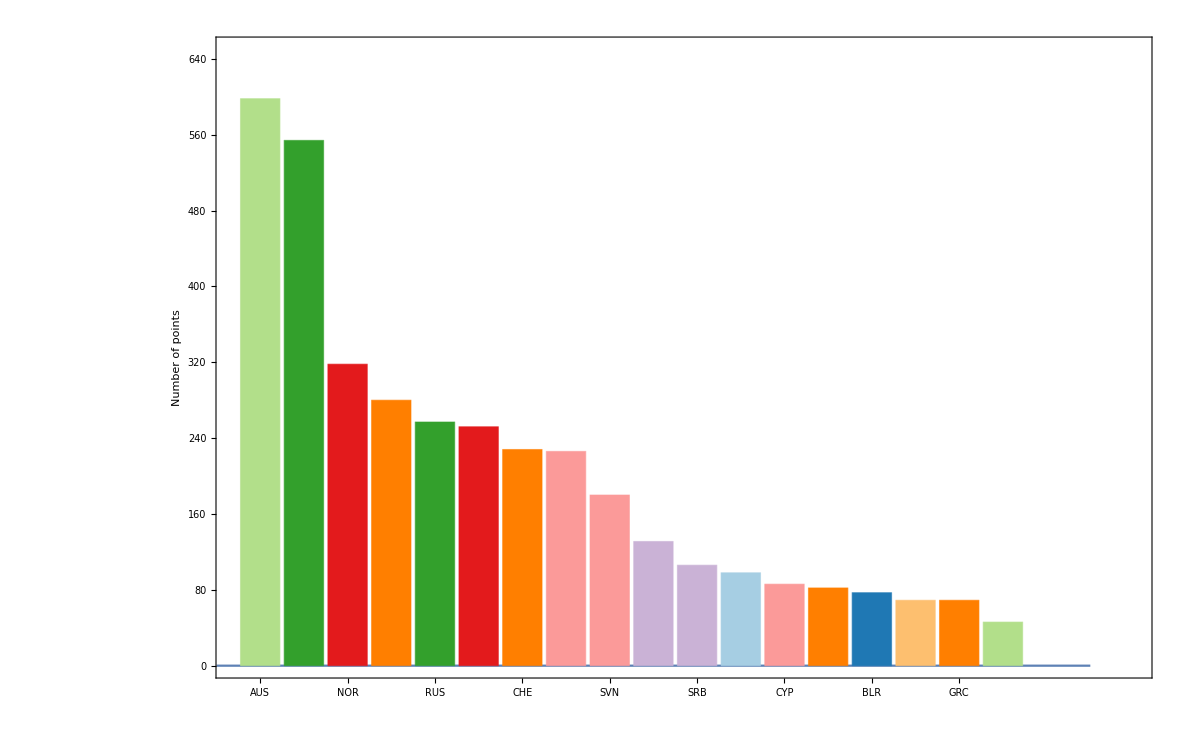

```mathematica
FinalSite=Show[Plot[0,{x,0,20},GridLines->{{},{}},GridLinesStyle->Directive[Black,Dashed,Thick], PlotRange->{{0.4,21},{0,650}},ImageSize->1200,AxesOrigin->{0,0},{FrameTicks->{{Automatic,None},{Table[{i,Style[StringTake[FinalPointsWithDeduction[[i,1]],{2,4}],Bold],{0.00,0},Dashing[1]},{i,Length[FinalPointsWithDeduction]}],None}},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{Black,25,FontFamily->"Helvetica"}},FrameLabel->{"","Number of points","Predicted number of points in Eurovision 2019 final"}],BarChart[FinalPointsWithDeduction[[All,2]],ChartStyle->{Table[If[MemberQ[Q2,i],EdgeForm[{Dashing[2],Thick}],EdgeForm[{Dashing[2],Thick}]],{i,20}],ColorsFinal},ImageSize->1200,BaseStyle->{FontFamily->"Helvetica",18},Frame->True,FrameStyle->Directive[Thick,Dashing[2]]]]
```

```mathematica
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/FinalSitePlus200.png",FinalSite,ImageResolution->200];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/FinalSitePlus100.png",FinalSite,ImageResolution->100];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/FinalSitePlus50.png",FinalSite,ImageResolution->50];
```

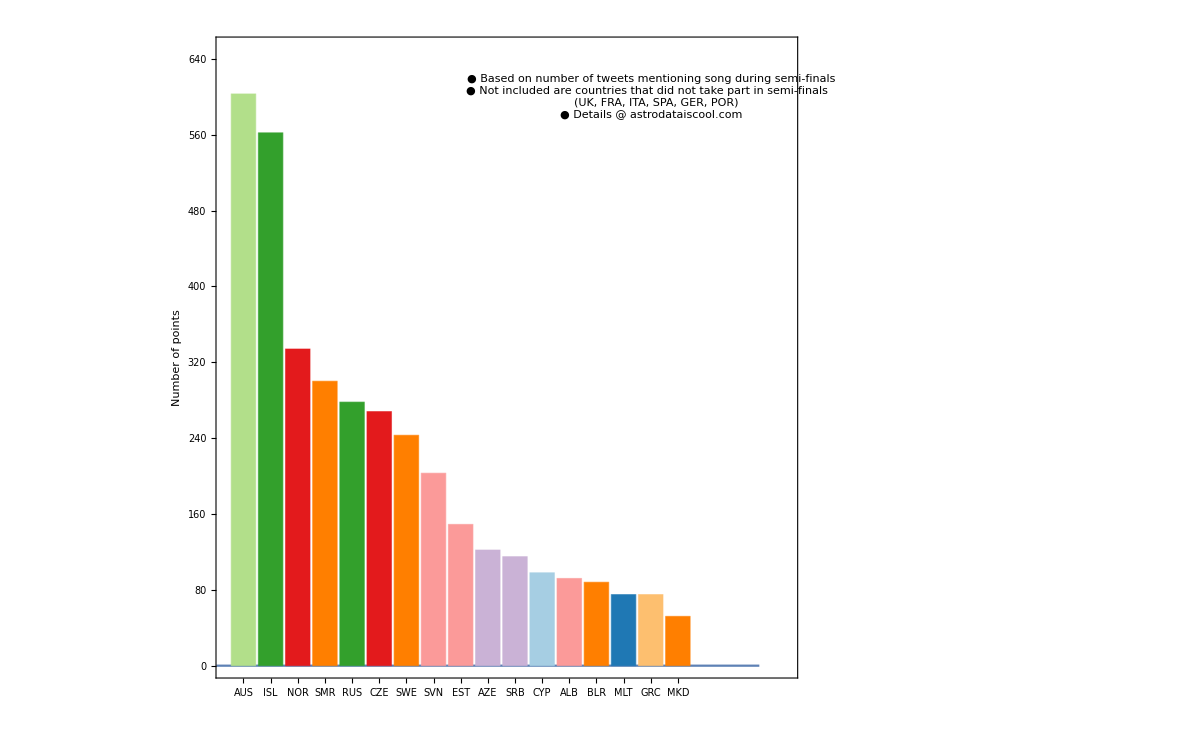

```mathematica
FinalOutsideWorld=Show[Plot[0,{x,0,20},GridLines->{{},{}},GridLinesStyle->Directive[Black,Dashed,Thick], PlotRange->{{0.4,21},{0,650}},ImageSize->1200,AxesOrigin->{0,0},{FrameTicks->{{Automatic,None},{Table[{i,Style[StringTake[FinalPointsWithDeduction[[i,1]],{2,4}],Bold],{0.00,0},Dashing[1]},{i,Length[FinalPointsWithDeduction]}],None}},Frame->True,FrameStyle->Directive[Thick,Dashing[2]],FrameTicksStyle->Directive[20],LabelStyle->{Black,25,FontFamily->"Helvetica"}},FrameLabel->{"","Number of points","Predicted number of points in Eurovision 2019 final"},Epilog->Inset[Grid[{{Text[Style["● Based on number of tweets mentioning song during semi-finals",FontSize->15,Plain,Black,FontFamily->"Helvetica"]]},{Text[Style["● Not included are countries that did not take part in semi-finals  ",FontSize->15,Plain,Black,FontFamily->"Helvetica"]]},{Text[Style["    (UK, FRA, ITA, SPA, GER, POR) ",FontSize->15,Plain,Black,FontFamily->"Helvetica"]]},{Text[Style["● Details @ astrodataiscool.com  ",FontSize->15,Plain,Black,FontFamily->"Helvetica"]]}},Spacings->{0,0},Alignment-> Left],{16,600}]],BarChart[FinalPointsWithDeduction[[All,2]],ChartStyle->{Table[If[MemberQ[Q2,i],EdgeForm[{Dashing[2],Thick}],EdgeForm[{Dashing[2],Thick}]],{i,20}],ColorsFinal},ImageSize->1200,BaseStyle->{FontFamily->"Helvetica",18},Frame->True,FrameStyle->Directive[Thick,Dashing[2]]]]
```

```mathematica
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/FinalOutsidePlus200.png",FinalOutsideWorld,ImageResolution->200];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/FinalOutsidePlus100.png",FinalOutsideWorld,ImageResolution->100];
Export["/Users/nevencaplar/Documents/Small/Eurovision2019/FinalOutsidePlus50.png",FinalOutsideWorld,ImageResolution->50];
```